Hay que editar los valores de $NLHome (carpeta del ejecutable de netlogo) y $NLModel (carpeta donde está) con los de la máquina local.

```mathematica
<<NetLogo`
$NLHome= "/opt/netlogo-4.0.5";
$NLModel="/home/erikasv/github/Collective-intelligence--Analysis-and-modeling";
NLStart[];
NLCommand["no-display"];
NLLoadModel[ToFileName[{$NLModel},"modelo.nlogo"]];
```

```mathematica
Experiment1[p_]:=Module[{},
NLCommand["set num-people ",p,"setup"];
Mean[NLDoReport["go","clustering-coefficient",100]]
];
people=Table[i,{i,10,1000,10}];
NLCommand["no-display"];
clusteringData=Map[Experiment1,people];
```

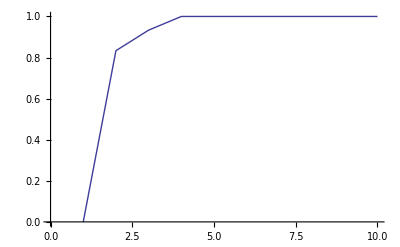

```mathematica
ListPlot[clusteringData,Joined->True]
```

```mathematica
Experiment2[p_]:=Module[{},
NLCommand["set num-people ",p, "set reduce-documents? True", "set vote-threshold 3","setup"];
Mean[NLDoReport["go","clustering-coefficient",10]]
];
```

```mathematica
people=Table[i,{i,10,10000,10}];
NLCommand["no-display"];
clusteringData1=Map[Experiment2,people];
```

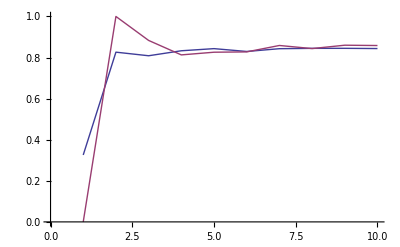

```mathematica
ListPlot[{clusteringData,clusteringData1},Joined->True,PlotRange->{{0,10},{0.,1}}]
```

```mathematica
hola
```

hola